```mathematica
c = 1;


fOld[x_]:=(1/4)x^4-(1/2)c^2 x^2
f[x_]:=-((1/4)*x^3)/24+x
```

```mathematica
integrand[y_,eps_, lower_]:=-NIntegrate[Exp[-f[z]/eps],{z,y,lower}]
(*firstIntegral[x_,eps_]:=NIntegrate[Exp[f[z]/eps],{z,6,x}]*)
```

```mathematica
ExpTime[sta_,arr_,eps_]:=(1/eps)*NIntegrate[(Exp[f[w]/eps])*integrand[w,eps, 0],{w,sta, arr}]
```

```mathematica
ExpTime[0,6,0.01]
```

NIntegrate::nlim: z = w is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

2.50744×10^163

```mathematica
saddapproxSecond[eps_]:=Exp[-f[c]/eps]*Sqrt[(2*π*eps)/(2)]
saddapproxFirst[eps_]:=Exp[f[0]/eps]*Sqrt[(2*π*eps)/(1)]
```

```mathematica
tempe={0.0001,0.001, 0.01,0.1, 0.5,1};

secondIntegralExact =Table[integrand[0.0,eps, 0], {eps, tempe}]
secondIntegralLaplace =Table[saddapproxSecond[eps], {eps, tempe}]//N

firstIntegralExact =Table[firstIntegral[1,eps], {eps, tempe}]
firstIntegralLaplace =Table[saddapproxFirst[eps], {eps, tempe}]
```

{0.,0.,0.,0.,0.,0.}

{3.4895099050437×10^-4300,9.50591411687367×10^-432,1.8686×10^-44,0.0000282403,0.173188,0.658877}

{5.2431935945971×10^4293,6.08611909336367×10^426,9.785×10^40,2036.72,3.60111,2.34574}

{0.0250663,0.0792665,0.250663,0.792665,1.77245,√(2 π)}

```mathematica
Plot[{f[z]/1, (z-1)^2-1/4},{z,0,3}];
```

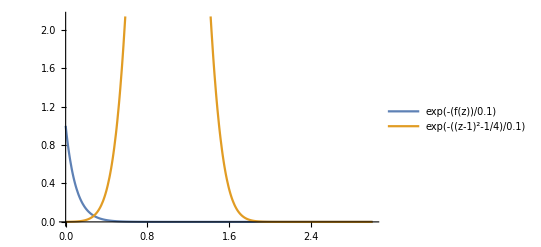

```mathematica
Plot[{Exp[-f[z]/0.1],Exp[-((z-1)^2-1/4)/0.1]},{z,0,3}, PlotLegends->"Expressions"]
```

```mathematica
(*Plot[ExpTime[x,-1,0.01],{x,-0.5,0.5}]*)
```

```mathematica
kramapprox[eps_]:= Exp[0.25/eps]*Sqrt[(2*π)^2/(2)]
```

```mathematica
(*Plot[{Log[kramapprox[1/beta]],ExpTime[0.75,-1,1/beta]},{beta,1,4}]*)
```

```mathematica
$Aborted
```

$Aborted

```mathematica
tem={0.1,0.2, 0.35,0.5, 0.6,0.7,1.0, 1.2, 1.4, 2, 2.5};
saddleapprox =Table[kramapprox[eps], {eps, tem}]
```

{54.1254,15.5072,9.0756,7.32508,6.73939,6.34995,5.70477,5.47196,5.3115,5.03445,4.91015}

```mathematica
exact=Table[ExpTime[0,10,eps],{eps,tem}]
```

NIntegrate::nlim: z = w is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{3.19313×10^16,2.93272×10^8,121056.,5784.64,1821.28,809.526,195.718,114.162,77.7662,38.3057,26.8319}

```mathematica
Log[exact]
```

{38.0024,19.4966,11.704,8.66296,7.5073,6.69645,5.27667,4.73762,4.35371,3.6456,3.28959}

```mathematica
Log[saddleapprox]
```

{3.9913,2.7413,2.20559,1.9913,1.90797,1.84845,1.7413,1.69964,1.66987,1.6163,1.5913}

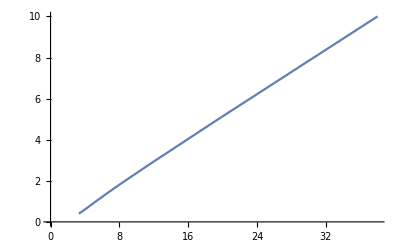

```mathematica
ListLinePlot[Transpose[{Log[exact],1/tem}]]
```

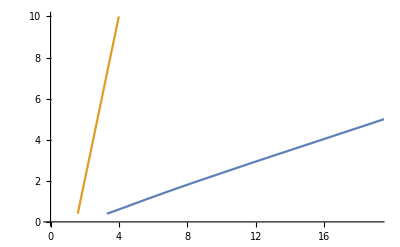

```mathematica
ListLinePlot[{Transpose[{Log[exact],1/tem}], Transpose[{Log[saddleapprox],1/tem}]}]
```

```mathematica
1/tem
```

{10.,5.,2.85714,2.,1.66667,1.42857,1.,0.833333,0.714286,1/2,0.4}

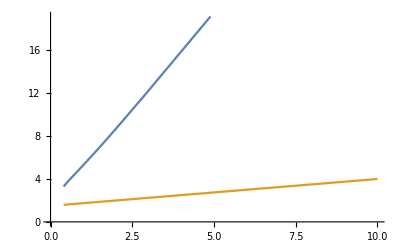

```mathematica
ListLinePlot[{Transpose[{1/tem, Log[exact]}], Transpose[{1/tem,Log[saddleapprox]}]}]
```

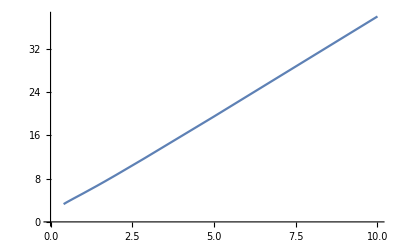

```mathematica
ListLinePlot[Transpose[{1/tem, Log[exact]}]]
```